```mathematica
particleRadius=2;
xRange= 25;
xInterval=10;
yRange=6;

dashSettingLine=Dashing[0.02];
thicknessSettingLine=Thickness[0.01];
```

```mathematica
particle=Graphics[{EdgeForm[{Gray,Thickness[0.005]}],White,{Table[Disk[{x,yRange},particleRadius],{x,-xRange,xRange,xInterval}],Table[Disk[{x,-yRange},particleRadius],{x,-xRange,xRange,xInterval}]}}];
bp=Graphics[{dashSettingLine,thicknessSettingLine,Table[Line[{{-l,-6},{-l,6}}],{l,-xRange,xRange,xInterval}]}];
bb=Graphics[{thicknessSettingLine,{Line[{{-25,6},{25,6}}],Line[{{-25,-6},{25,-6}}]}}];

Show[bp,bb,particle]
```

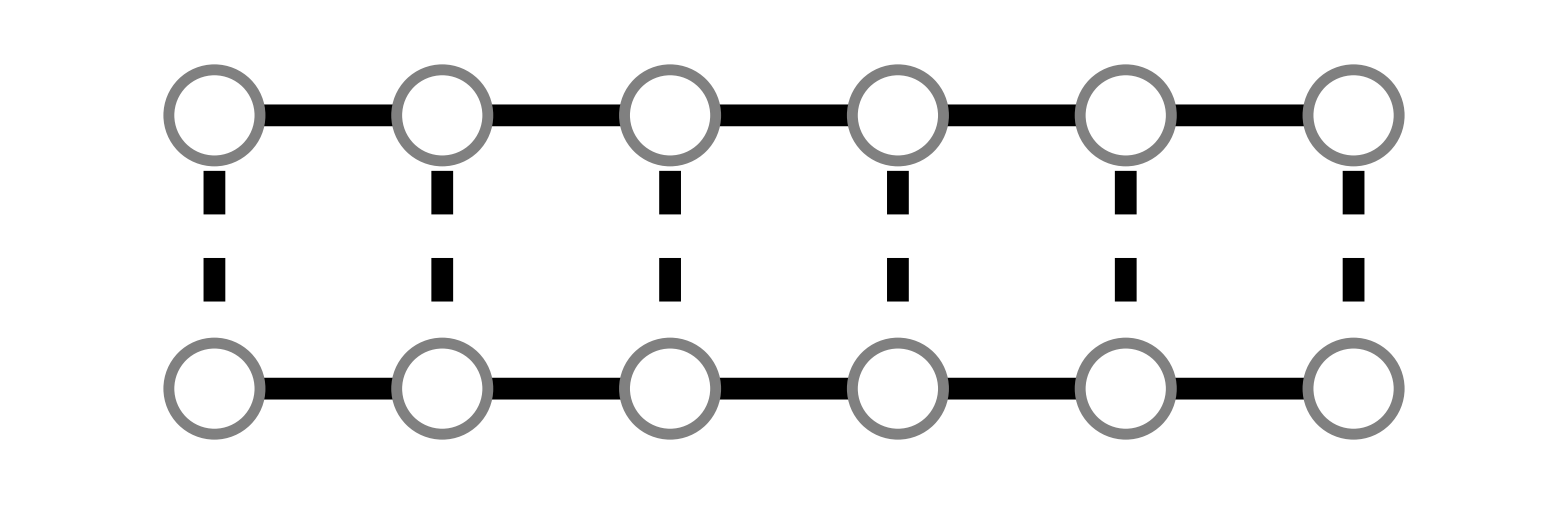

```mathematica
particleRadius=2;
xRange= 25;
xInterval=10;
yRange=6;

dashSettingLine=Dashing[0.02];
thicknessSettingLine=Thickness[0.01];
```

```mathematica
particle=Graphics[{EdgeForm[{Gray,Thickness[0.005]}],White,{Table[Disk[{x+5,yRange},particleRadius],{x,-xRange,xRange,xInterval}],Table[Disk[{x,-yRange},particleRadius],{x,-xRange,xRange,xInterval}]}}];
bp=Graphics[{dashSettingLine,thicknessSettingLine,Table[Line[{{-l,-6},{-l+5,6}}],{l,-xRange,xRange,xInterval}]}];
bb=Graphics[{thicknessSettingLine,{Line[{{-20,6},{30,6}}],Line[{{-25,-6},{25,-6}}]}}];
Magnify[Rasterize[Show[bp,bb,particle],ImageResolution->600],5]
```

-Graphics-

```mathematica
particle=Graphics[{EdgeForm[{Gray,Thickness[0.005]}],White,{Table[Disk[{x+5,yRange},particleRadius],{x,-xRange,xRange,xInterval}],Table[Disk[{x,-yRange},particleRadius],{x,-xRange,xRange,xInterval}]}}];
bp=Graphics[{dashSettingLine,thicknessSettingLine,Table[Line[{{-l,-6},{-l+5,6}}],{l,-15,xRange,xInterval}]}];
bb=Graphics[{thicknessSettingLine,{Line[{{-20,6},{30,6}}],Line[{{-25,-6},{25,-6}}]}}];
Magnify[Rasterize[Show[bp,bb,particle],ImageResolution->600],5]
```

-Graphics-

```mathematica
particle=Graphics[{EdgeForm[{Gray,Thickness[0.005]}],White,{Table[Disk[{x+5,yRange},particleRadius],{x,-xRange,xRange,xInterval}],Table[Disk[{x,-yRange},particleRadius],{x,-xRange,xRange,xInterval}]}}];
bp=Graphics[{dashSettingLine,thicknessSettingLine,Table[Line[{{-l,-6},{-l+5,6}}],{l,-5,xRange,xInterval}]}];
bb=Graphics[{thicknessSettingLine,{Line[{{-20,6},{30,6}}],Line[{{-25,-6},{25,-6}}]}}];
Magnify[Rasterize[Show[bp,bb,particle],ImageResolution->600],5]
```

-Graphics-

```mathematica
particle=Graphics[{EdgeForm[{Gray,Thickness[0.005]}],White,{Table[Disk[{x+5,yRange},particleRadius],{x,-xRange,xRange,xInterval}],Table[Disk[{x,-yRange},particleRadius],{x,-xRange,xRange,xInterval}]}}];
bp=Graphics[{dashSettingLine,thicknessSettingLine,{Line[{{-25,-6},{-20,6}}],Line[{{-15,-6},{-10,6}}],Line[{{15,-6},{20,6}}],Line[{{25,-6},{30,6}}]}}];
bb=Graphics[{thicknessSettingLine,{Line[{{-20,6},{30,6}}],Line[{{-25,-6},{25,-6}}]}}];
Magnify[Rasterize[Show[bp,bb,particle],ImageResolution->600],5]
```

-Graphics-

```mathematica
particle=Graphics[{EdgeForm[{Gray,Thickness[0.005]}],White,{Table[Disk[{x+5,yRange},particleRadius],{x,-xRange,xRange,xInterval}],Table[Disk[{x,-yRange},particleRadius],{x,-xRange,xRange,xInterval}]}}];
bp=Graphics[{dashSettingLine,thicknessSettingLine,{Line[{{-25,-6},{-20,6}}],Line[{{-15,-6},{-10,6}}],Line[{{5,-6},{10,6}}],Line[{{15,-6},{20,6}}],Line[{{25,-6},{30,6}}]}}];
bb=Graphics[{thicknessSettingLine,{Line[{{-20,6},{30,6}}],Line[{{-25,-6},{25,-6}}]}}];
Magnify[Rasterize[Show[bp,bb,particle],ImageResolution->600],5]
```

-Graphics-

```mathematica
particle3D=Graphics3D[{Table[Sphere[{x,0,4}],{x,-15,15,5}],Table[Sphere[{x,0,-4}],{x,-15,15,5}]},Boxed->False];
bb3D=Graphics3D[{Gray,{Cylinder[{{-15,0,4},{15,0,4}},0.3],Cylinder[{{-15,0,-4},{15,0,-4}},0.3]},Boxed->False}];
bp3D=Graphics3D[{EdgeForm[None],Gray,Table[Table[Cylinder[{{x,0,(z+0.4)},{x,0,z}},0.3],{z,-4,4,1}],{x,-15,15,5}],Boxed->False}];
Magnify[Rasterize[Show[particle3D,bb3D,bp3D],ImageResolution->600],5]
```

-Graphics-

```mathematica
d=0.31;
Sparticle3D=Graphics3D[{Table[Sphere[{x,0,4}],{x,-10,20,5}],Table[Sphere[{x,0,-4}],{x,-15,15,5}]},Boxed->False];
Sbb3D=Graphics3D[{Gray,{Cylinder[{{-10,0,4},{20,0,4}},0.3],Cylinder[{{-15,0,-4},{15,0,-4}},0.3]},Boxed->False}];
Sbp3D=Graphics3D[{EdgeForm[None],Gray,Table[{Cylinder[{{i,0,-4},{i+d,0,-4+0.5}},0.3],Cylinder[{{i+2d,0,-3},{i+3d,0,-3+0.5}},0.3],Cylinder[{{i+4d,0,-2},{i+5d,0,-2+0.5}},0.3],Cylinder[{{i+6d,0,-1},{i+7d,0,-1+0.5}},0.3],Cylinder[{{i+8d,0,0},{i+9d,0,0+0.5}},0.3],Cylinder[{{i+10d,0,1},{i+11d,0,1+0.5}},0.3],Cylinder[{{i+12d,0,2},{i+13d,0,2+0.5}},0.3],Cylinder[{{i+14d,0,3},{i+15d,0,3+0.5}},0.3],Cylinder[{{i+16d,0,4},{i+17d,0,4+0.5}},0.3]},{i,-15,15,5}]}];
Magnify[Rasterize[Show[Sparticle3D,Sbb3D,Sbp3D],ImageResolution->600],5]
```